# C & Q Chaos II - Integrable Hamiltonian systems

In this notebook, we will explore integrable Hamiltonian systems. 

We will see that they have stable and unstable fixed points connected by stable and unstable manifolds: 
 - When a manifold is both stable and unstable, it is known as a homoclinic or heteroclinic manifold. This concept will be very important later. 
 - It turns out that these manifolds also play an important role as separatrices  (singular: separatrix), manifolds that separate between different types of motion.

We will also explore the concept of integrable systems: 
  - An autonomous Hamiltonian system of a single degree of freedom (DOF) is always integrable, since the motions stay on surfaces constant energy. 
  - Interestingly, a time-dependent Hamiltonian can be viewed as an autonomous system with two DOFs with time being a formal coordinate. 
  - Integrable Hamiltonian systems can be qualitatively understood as a “product” of motions generated by 1DOF Hamiltonians.
  - The “product” intuition is formalized by the notion of separability and Liouville integrability.
  - Real systems demonstrate that the “product” notion and separability can be strongly warped and hidden from view. 

Few-degree-of-freedom systems become increasingly harder to analyze. We will mainly focus on autonomous 2DOF systems in this course:
   - In that case, we can use the method of Poincaré surfaces of section. These “cut” though the flow of the evolution through phase space and provide insight into the dynamics.
   -  The 2DOF systems also provide the “minimal” example where chaos occurs. (But more about that next time.)

## Mathematical pendulum and its equilibria

(Here we finish the mathematical pendulum chapter that we did not finish in the first session.)

```mathematica
-Graphics-;
Clear[H]
H[p_,x_] := 1/2 p^2 - Cos[x];
(*Again special units for simplicity. The phase-space is 2π-periodic in x. x=0 is the equilibrium position, x=±π is the upright position.*)
```

#### Repurpose your code from the first lesson to briefly explore the mathematical pendulum

#### Show solution

```mathematica
EOM = {x'[t]==(D[H[p,x],p]/.{x->x[t],p->p[t]}),p'[t] == (-D[H[p,x],x]/.{x->x[t],p->p[t]})}
x0 = 2.5; 
p0=0;
Init ={x[0] == x0,p[0]==p0} ;
Evolution =NDSolve[Join[EOM,Init],{x[t],p[t]},{t,0,20}]
Plot[x[t]/.Evolution[[1]],{t,0,10}]
ParametricPlot[{x[t],p[t]}/.Evolution[[1]],{t,0,15}]
ContourPlot[H[p,x],{x,-π,π},{p,-π,π},Contours->20] (*Contour plot of all energy levels.*)
E0 = H[p0,x0] (*Energy of initial conditions above.*)
ContourPlot[H[p,x]==E0,{x,-π,π},{p,-π,π}] (*In this case (autonomous Hamiltonian system with 1 degree of freedom) we were able to find the shape of the trajectory in phase space by finding the energy hypersurface.*)
```

#### Assume you don’t know anything about the function Cos[x]. Classify the extrema of the potential on the interval x ∈ [-π,π], find the corresponding energies.

#### Show solution

```mathematica
(*There are several ways to do this. Below is the analytical approach.*)
V[x_]:=-Cos[x];
extrema = Solve[D[V[x],x]==0&&-π<=x<=π,x]
(*Note that x=π and x=-π correspond to the same point!*)
Energies = V[x]/.extrema
```

#### Expand potential around the maximum up to δx^2 using Series[] (and truncate using Normal[]).

#### Show solution

```mathematica
VSer = Series[V[π+δx],{δx,0,2}]
VTrunc = Normal[VSer]
(*The two outputs may not look that different, but VSer is a "SeriesData[]" object, VTrunc is a normal expression.*)
FullForm[VSer]
FullForm[VTrunc]
```

#### Find equations of motion for the particle at the unstable energy near the potential.

#### Show solution

```mathematica
Htrunc[δp_,δx_]:= 1/2 δp^2 + 1-δx^2/2;
TrajRule = {δx->δx[t],δp->δp[t]}; (*To avoid writing it twice*)
EOMtrunc = {δx'[t]==(D[Htrunc[δp,δx],δp]/.TrajRule ),δp'[t]==-(D[Htrunc[δp,δx],δx]/.TrajRule )}
```

#### Solve the approximate equations of motion for general initial conditions

#### Show solution

```mathematica
(*Let's try DSolve*)
truncSol = DSolve[Join[EOMtrunc,{δp[0]==δp0,δx[0]==δx0}],{δx[t],δp[t]},t]
truncSol//ExpandAll
Collect[%,ⅇ^t]
```

#### Generate a list of rules for a number of initial conditions within a circle of some radius from δp=0, δx=0 and visualize them

#### Show solution

```mathematica
InitConds = Table[{δp0->0.01j Sin[i π/8],δx0->0.01j Cos[i π/8]},{i,1,16},{j,1,4}]
(*Visualize initial conditions*)
ListPlot[{δp0,δx0}/.InitConds,AspectRatio->1, AxesLabel->{δp0,δx0}]
```

#### Plot the evolutions given the initial conditions from above. (Bonus: overlay the evolutions with the original initial conditions by using Show[].)

#### Show solution

```mathematica
truncEvols = truncSol[[1]]/.InitConds;
(*show one row:*)
truncEvols[[2]]
```

```mathematica
Show[ParametricPlot[{δp[t],δx[t]}/.truncEvols,{t,0,1},AspectRatio->1, AxesLabel->{δp,δx}],ListPlot[{δp0,δx0}/.InitConds,AspectRatio->1, AxesLabel->{δp0,δx0},PlotStyle->Red]]
```

## More on the unstable equilibrium

```mathematica
(*Obviously there are stable and unstable directions*)
 truncSol[[1]]/.{δp0->un,δx0->un}
 truncSol[[1]]/.{δp0->-st,δx0->st}
(*Unless you exactly hit the condition δp0 == -δx0, the exponentially growing solution will always be represented and it will quickly dominate. *)
```

The point δx0 = δp0 = 0 is an unstable fixed point of the system . The full non - truncated prolongations of the δp0 == -δx0 manifold is the stable manifold of the fixed point . The δp0 == δx0 prolongation would be known as the unstable manifold of the fixed point. The formal definition is that the points on the stable/unstable manifold approach the fixed point as t-> ±∞. 

For the mathematical pendulum these appear along E=1.  Interestingly enough, the full unstable/stable manifolds are the same under the periodic identification! This is known as a homoclinic manifold (a manifold whose points evolve to the same fixed point as both t-> ±∞.)

```mathematica
ContourPlot[H[p,x]==1,{x,-π,π},{p,-π,π}]
```

Note that the homoclinic manifold acts as a separatrix that separates bound motion (“libration”) from unbound motion (“rotation”)

```mathematica
Show[ContourPlot[H[p,x],{x,-2π,2π},{p,-π,π},Contours->20,AspectRatio->1/2,FrameLabel->{"x","p"}] ,ContourPlot[H[p,x]==1,{x,-2π,2π},{p,-π,π}],VectorPlot[{D[H[p,x],p],-D[H[p,x],x]},{x,-2π,2π},{p,-π,π}],VectorPlot[{p,-Sin[x]},{x,-2π,2π},{p,-π,π},VectorColorFunction->None,VectorPoints->Fine,VectorStyle->Black,VectorSizes->Tiny]]
```

## A time - dependent Hamiltonian

```mathematica
(*A simple Hamiltonian for the pendulum driven by a harmonically varrying force.*)
```

```mathematica
Hna[p_,x_,t_] :=  1/2 p^2 - Cos[x] +ϵ Cos[x] Sin[t];
(*(You can write Greek symbols by hitting escape, writing the name of the symbol and hitting escape again.)*)
(*The force is a function of the height of the pendulum, ϵ is assumed to be "small". As long as ϵ<1, the force will never dominate over the pendulum.*)
```

### Rewrite the system as an autonomous 2DOF system

#### Try to find a Hamiltonian H_τ(p_τ,τ) with a pair of canonical coordinates τ,p_τ such that dτ/dt=1, and dp_τ/dt=0

#### Solution

```mathematica
Hτ[pτ_,τ_] := pτ;
EOMτ = {τ'[t] == D[Hτ[pτ,τ],pτ],pτ'[t] == -D[Hτ[pτ,τ],τ]}
(*Obviously, τ=t up to an integration constant.*)
```

#### Now try to find a reexpression of Hna(p,x,t) so that Hnaτ(p,x,pτ,τ) generates the same motion as Hna(p,x,t)

#### Solution

```mathematica
Hnaτ[p_,x_,pτ_,τ_] :=  1/2 p^2 - Cos[x] +ϵ Cos[x] Sin[τ] + pτ;
```

Notice that the dynamics are periodic in τ with a period 2 π . It is natural to consider the coordinate τ as 2 π - periodic then. The coordinate τ can be viewed as the relative phase with respect to the forcing in which we find the system. It is also interesting to note that in that case the motions can be viewed as occurring in a bounded (compact) region of phase space.

### Explore the dynamics of the system

#### Derive the equations of motion, integrate and plot a sample evolution

#### Solution

```mathematica
TrajRule = {p->p[t],x->x[t],pτ->pτ[t],τ->τ[t]}
(*Pro tip, do not want to type this repetitive structure over and over? Then just provide a list of canonical coordinates and use Table[].*)
CanCList = {p,x,pτ,τ};
TrajRule = Table[CanCList[[i]]->CanCList[[i]][t],{i,1,Length[CanCList]}]
```

```mathematica
EOM = {p'[t] == (-D[Hnaτ[p,x,pτ,τ],x]/.TrajRule),pτ'[t] == (-D[Hnaτ[p,x,pτ,τ],τ]/.TrajRule),x'[t]==(D[Hnaτ[p,x,pτ,τ],p]/.TrajRule),τ'[t] == (D[Hnaτ[p,x,pτ,τ],pτ]/.TrajRule)}
```

```mathematica
(*Initial conditions for a pendulum halfway between the top *)
Init = {p[0]==0,pτ[0]==0,τ[0]==0,x[0]==π/2}
```

```mathematica
ϵ0 = 0.3;
sampleSol = Block[{ϵ=ϵ0},NDSolve[Join[EOM,Init],{p,pτ,x,τ},{t,0,20π}]]
(*Block[] allows you to define a local value of a variable. This is helpful when wanting to evaluate an expression for a certain value of a free parameter without breaking things.*)
```

```mathematica
Plot[p[t]/.sampleSol,{t,0,20π},AxesLabel->{"t","p"}]
Plot[pτ[t]/.sampleSol,{t,0,20π},AxesLabel->{"t","pτ"}]
Plot[x[t]/.sampleSol,{t,0,20π},AxesLabel->{"t","x"}]
Plot[τ[t]/.sampleSol,{t,0,20π},AxesLabel->{"t","τ"}]
```

#### What is the meaning of pτ? Check that our new Hamiltonian is conserved up to numerical noise. Use the fact to interpret pτ

#### Solution

```mathematica
(*Plot evolution of Hamiltonian function:*)
Plot[(Hnaτ[p,x,pτ,τ]/.{ϵ->ϵ0})/.TrajRule/.sampleSol,{t,0,20π},AxesLabel->{"t","Formal Hamiltonian"}]
(*Look at the scale!*)
```

```mathematica
Plot[-pτ/.TrajRule/.sampleSol,{t,0,20π},AxesLabel->{"t","-p_τ"}]
Plot[(1/2 p^2 - Cos[x] +ϵ0 Cos[x] Sin[t] )/.TrajRule/.sampleSol,{t,0,20π},AxesLabel->{"t","Original Hamiltonian/energy"}]
```

Takeaway: You can extend your phase space to have time and minus the physical energy as a new pair of canonical coordinates! (This should be familiar to relativists.)

#### Try this method of visualizing the dynamics: capture the values of p and x after every 2π -time period of the forcing using the Reap[...] and WhenEvent. Plot 100 such points.

#### Solution

```mathematica
pxVals = Block[{ϵ=ϵ0},Reap[NDSolve[Join[EOM,Init,{WhenEvent[Mod[τ[t],2π]==0,Sow[{Mod[x[t]+π,2π]-π,p[t]}]]}],{p,pτ,x,τ},{t,0,200π}]]]
(*We store the evolution of x assuming it is 2π-periodic and runs between -π,π*)
ListPlot[pxVals[[2,1]],AspectRatio->1,AxesLabel->{"x","p"}]
```

```mathematica
(*Let us take a look at the snapshot evolution*)
Manipulate[ListPlot[Take[pxVals[[2,1]],n],AspectRatio->1,AxesLabel->{"x","p"},PlotRange->{{-π,π},{-π,π}}],{n,1,99,1}]
```

#### Write a function using Module[] that provides n snapshots given initial conditions and ϵ.

#### Solution

```mathematica
SnapSet[Init_,n_,ϵ0_] := Module[{pxSet},
pxSet = Block[{ϵ=ϵ0},Reap[NDSolve[Join[EOM,Init,{WhenEvent[Mod[τ[t],2π]==0,Sow[{Mod[x[t]+π,2π]-π,p[t]}]]}],{p,pτ,x,τ},{t,0, 2n π}]]];
pxSet[[2,1]]
]
```

#### Create a set of initial conditions to probe the dynamics. Generate initial conditions that would correspond both to librations and rotations for the unperturbed pendulum.

#### Solution

```mathematica
imax=50;
(*We know that for the unperturbed pendulum the separatrix was at E=1. This corresponds to, e.g. x=0 and p=√2. We can than take a look at initial conditions starting from p=0 and going over √2>*)
InitTable = Table[{p[0]==0+2.5 i/imax,pτ[0]==0,τ[0]==0,x[0]==0},{i,1,imax}]
```

#### Find snapshot evolutions for this range of initial conditions and plot them in a single plot

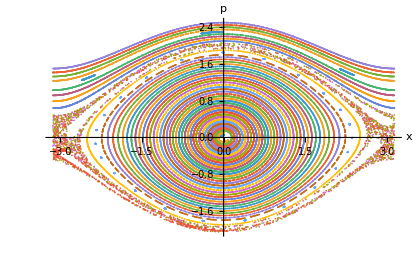

```mathematica
Snaps = Table[SnapSet[InitTable[[i]],1000,0.01],{i,1,imax}]
ListPlot[Snaps,AxesLabel->{"x","p"}]
```

What just happened?

```mathematica
ListPlot[SnapSet[{p[0]==1.9500000000000002,pτ[0]==0,τ[0]==0,x[0]==0},100000,0.01],AxesLabel->{"x","p"},PlotRange->{{2.5,π},{-1,1}}]
```

## Take a step back: Integrable systems

- Every 1 DOF autonomous system is integrable - the shape of its phase - space trajectories are simply given by constant energy surfaces .
 - If we just add N 1DOF Hamiltonians that depend on independent DOFs, the result will again be integrable . E . g . for N=2 DOFs :

```mathematica
Hsep[px_,x_,py_,y_] := Hx[px,x] + Hy[py,y];
```

- Then the pairs of coordinates fulfill equations that are not coupled and the Hamiltonians Hx, Hy are conserved separately.

```mathematica
px'==-D[Hsep[px,x,py,y],x]
x'==D[Hsep[px,x,py,y],px]
py'==-D[Hsep[px,x,py,y],y]
y'==D[Hsep[px,x,py,y],py]
```

- For bound motions, the motions are oscillations in N different DOFs. Since each oscillation is a topological circle, the composite motion is a product of N circles. That is known as an N-torus.
- Is every integrable Hamiltonian like this? In a way yes, but seeing it from the actual expression of the Hamiltonian can be hard.

### Simple example: Motion in a central potential

Consider motion in a plane in a radial potential.

```mathematica
Hc[px_,x_,py_,y_] := 1/2(px^2+py^2) + Pot[√(x^2+y^2)];
```

Is this Hamiltonian separable at face value? No, but it is integrable as we will see .

#### Transform the Hamiltonian to polar coordinates

(Recall that momenta are forms, not vectors, they transform with an inverse Jacobian.)

#### Solution

```mathematica
xpol  = r Cos[ϕ];
ypol = r Sin[ϕ];
(*Find the Jacobian and inverse Jacobian of the transform:*)
J ={ {D[xpol,r],D[xpol,ϕ]},{D[ypol,r],D[ypol,ϕ]}}
iJ = Inverse[J]
{pxpol,pypol} = {pr,pϕ}.iJ//Simplify
 Hc[pxpol,xpol,pypol,ypol]//Simplify[#,{r>0}]&
```

```mathematica
Hpol[pr_,r_,pϕ_,ϕ_]:=1/2 (pr^2+pϕ^2/r^2+2 Pot[r]);
```

ϕ is a cyclical coordinate (the Hamiltonian is independent of it), so L =pϕ is conserved

#### The r,pr trajectory shape is determined by the condition that E=Hpol and L=pϕ are constant. Also, the ϕ,pϕ shape is trivially determined by this constraint. Plot some of the shapes using the potential below.

```mathematica
Pot[r_] := -1/r - 1/r^3;
```

#### Solution

```mathematica
ContourPlot[Hpol[pr,r,4,0],{r,1,50},{pr,-0.5,0.5},Contours->{-0.03,-0.025,-0.01,0,0.01,0.025},FrameLabel->{r,pr}]
DensityPlot[Hpol[pr,r,4,0],{r,1,50},{pr,-0.5,0.5}]
ContourPlot[pϕ,{ϕ,0,2π},{pϕ,0,5},FrameLabel->{ϕ,pϕ}]
```

```mathematica
Plot also the shape this defines in the ϕ,r,pr plane for a selected bound motion.Plot also the shape this defines in the ϕ,r,pr plane for a selected bound motion.
```

#### Plot the hypersurface defined by the E=const. L=const. condition in the r,pr,ϕ space for a suitable bound motion.

Hint: Try an embedding into Euclidean x,y,z where we remap r=√(x^2+y^2), ϕ=ArcTan[y,z], and pr=z.

#### Solution

```mathematica
ContourPlot3D[Hpol[z,Sqrt[x^2+y^2],4,ArcTan[y,x]]==-0.025,{x,-32,32},{y,-32,32},{z,-0.3,0.3}]
```

#### Now find also the corresponding r,pr,ϕ trajectory and plot it on top of the torus using ParametricPlot3D[] and Show[]

#### Solution

```mathematica
Traj = {pr->pr[t],r->r[t],ϕ->ϕ[t]};
EOM = {pr'[t]==(-D[Hpol[pr,r,pϕ,ϕ],r]/.Traj),r'[t]==(D[Hpol[pr,r,pϕ,ϕ],pr]/.Traj),ϕ'[t]==(D[Hpol[pr,r,pϕ,ϕ],pϕ]/.Traj)}
ri = 15; 
pϕi = 4;
E0 = -0.025;
initSol = Solve[Hpol[pr,ri,pϕi,ϕ]==E0,pr];
Init = {r[0]==ri,ϕ[0]==0,pr[0]==(pr/.initSol[[2]])}
TrSol =Block[{pϕ=pϕi},NDSolve[Join[EOM,Init],{r[t],pr[t],ϕ[t]},{t,0,100000}]]
```

```mathematica
ParametricPlot3D[{r[t]Cos[ϕ[t]],r[t]Sin[ϕ[t]],pr[t]}/.TrSol,{t,0,20000}]
Show[ContourPlot3D[Hpol[z,Sqrt[x^2+y^2],4,ArcTan[y,x]]==-0.025,{x,-32,32},{y,-32,32},{z,-0.3,0.3}],ParametricPlot3D[{r[t]Cos[ϕ[t]],r[t]Sin[ϕ[t]],pr[t]}/.TrSol,{t,0,20000}]]
```

#### Build and plot a different “snapshot set”, by recording r, pr when ϕ mod 2π == 0

#### Solution

```mathematica
RPrSnaps = Block[{pϕ = pϕi},Reap[ NDSolve[Join[EOM, Init,{WhenEvent[Mod[ϕ[t],2π]==0,Sow[{r[t],pr[t]}]]}], {r[t], pr[t], ϕ[t]}, {t, 0, 100000}]]]
```

```mathematica
ListPlot[RPrSnaps[[2,1]]]
```

This is closely analogous to the snapshots we did for the driven mathematical pendulum. However, here we see this amounts to a cross-section of the flow. In some sense, we did a slice through the torus plotted above. 

In principle, we could have chosen any other condition Ψ(r,pr,ϕ,pϕ)==0 which, when crossed, is used to record the state. This would simply lead to a slice of the structures by a different hypersurface. This type of condition is known as a Poincaré surface of section. It is really useful to dissect the dynamics of systems with 2DOFs (or “effectively 2DOFs”).

### Liouville integrability

An autonomous Hamiltonian system of N degrees of freedom is Liouville integrable if there exist N functionally independent constants of motion
F_1,F_2,... F_N​ where:
 - The gradients of the functions F_i are linearly independent almost everywhere.
 - The Poisson bracket of any pair of the constants of motion vanishes.
(Often one chooses F_1=H.)

Given the above is satisfied the Liouville-Arnold theorem states that:
 - The hypersurfaces defined by constant F_1,F_2,... F_N are topologically products of the real line and circles, corresponding to bounded motion and possibly unbounded motion. (For purely bounded motion we get a simple N-dimensional torus.)
 - The motion can be solved for by quadratures: one-dimensional integral expressions that often implicitly define the solution.
 - There exist pairs of local canonical coordinates J_i,ψ^i, i=1...N such that J_i represent an alternative set of constants of motion, the Hamiltonian is transformed into H(J_i) (no dependence on ψ^i), and ψ^i'= dH/dJ_i = Ω^i(J_j)=const. These are known as Action-Angle coordinates.

Some notes:
-  Finding the transformation to the full set of action-angle coordinates is often harder than finding the exact solution of the equations of motion themselves. However, finding just the angles is exactly as hard as just solving the equations of motion by quadrature.
- Angles are great for perturbation theory, and you do not use the actions for that!
- Actions are great because they represent gauge/coordinate invariants.
- The Ω^i are known as the fundamental frequencies of motion. They can be extracted numerically (or even experimentally) from the motion just by looking at harmonics of various time-series from the system. They are also gauge/coordinate invariant.